## Notes

```mathematica
Import["/Users/paul/Documents/Projects/Wolfram Research/Wolfram Summer School/WSS19/Git/Roger Yu/Generalization/IMG_1258.jpg"]
```

-Graphics-

```mathematica
Import["/Users/paul/Documents/Projects/Wolfram Research/Wolfram Summer School/WSS19/Git/Roger Yu/Generalization/IMG_1259.jpg"]
```

-Graphics-

## Code

```mathematica
Clear[Δmat,xs,ys,ℒ]
```

Explicit summation over a set of δ-function spikes located at {x_i,y_i}:

```mathematica
Δmat[{Lx_,Ly_}][x_List,y_List][{n_,m_},{np_,mp_}]:=∑_(i=1)^Length[xs] Sin[(n π x_⟦i⟧)/Lx]Sin[(m π y_⟦i⟧)/Ly]Sin[(np π x_⟦i⟧)/Lx]Sin[(mp π y_⟦i⟧)/Ly]
```

Alternatively,

```mathematica
Δmat[{Subscript[ℒ, x],Subscript[ℒ, y]}][{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]},{Subscript[y, 1],Subscript[y, 2],Subscript[y, 3]}][{1,1},{2,2}]
```

Sin[π x_1] Sin[2 π x_1] Sin[π y_1] Sin[2 π y_1]+Sin[π x_2] Sin[2 π x_2] Sin[π y_2] Sin[2 π y_2]+Sin[π x_3] Sin[2 π x_3] Sin[π y_3] Sin[2 π y_3]

```mathematica
ArrayFlatten[Outer[Δmat[{Subscript[ℒ, x],Subscript[ℒ, y]}][{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]},{Subscript[y, 1],Subscript[y, 2],Subscript[y, 3]}],Subscript[ℐ, 3],Subscript[ℐ, 3],2]]//TraditionalForm
```

(sin^2(π x_1) sin^2(π y_1)+sin^2(π x_2) sin^2(π y_2)+sin^2(π x_3) sin^2(π y_3) | sin^2(π x_1) sin(π y_1) sin(2 π y_1)+sin^2(π x_2) sin(π y_2) sin(2 π y_2)+sin^2(π x_3) sin(π y_3) sin(2 π y_3) | sin^2(π x_1) sin(π y_1) sin(3 π y_1)+sin^2(π x_2) sin(π y_2) sin(3 π y_2)+sin^2(π x_3) sin(π y_3) sin(3 π y_3) | sin^2(π x_1) sin(π y_1) sin(2 π y_1)+sin^2(π x_2) sin(π y_2) sin(2 π y_2)+sin^2(π x_3) sin(π y_3) sin(2 π y_3) | sin^2(π x_1) sin^2(2 π y_1)+sin^2(π x_2) sin^2(2 π y_2)+sin^2(π x_3) sin^2(2 π y_3) | sin^2(π x_1) sin(2 π y_1) sin(3 π y_1)+sin^2(π x_2) sin(2 π y_2) sin(3 π y_2)+sin^2(π x_3) sin(2 π y_3) sin(3 π y_3) | sin^2(π x_1) sin(π y_1) sin(3 π y_1)+sin^2(π x_2) sin(π y_2) sin(3 π y_2)+sin^2(π x_3) sin(π y_3) sin(3 π y_3) | sin^2(π x_1) sin(2 π y_1) sin(3 π y_1)+sin^2(π x_2) sin(2 π y_2) sin(3 π y_2)+sin^2(π x_3) sin(2 π y_3) sin(3 π y_3) | sin^2(π x_1) sin^2(3 π y_1)+sin^2(π x_2) sin^2(3 π y_2)+sin^2(π x_3) sin^2(3 π y_3)
sin(π x_1) sin(2 π x_1) sin^2(π y_1)+sin(π x_2) sin(2 π x_2) sin^2(π y_2)+sin(π x_3) sin(2 π x_3) sin^2(π y_3) | sin(π x_1) sin(2 π x_1) sin(π y_1) sin(2 π y_1)+sin(π x_2) sin(2 π x_2) sin(π y_2) sin(2 π y_2)+sin(π x_3) sin(2 π x_3) sin(π y_3) sin(2 π y_3) | sin(π x_1) sin(2 π x_1) sin(π y_1) sin(3 π y_1)+sin(π x_2) sin(2 π x_2) sin(π y_2) sin(3 π y_2)+sin(π x_3) sin(2 π x_3) sin(π y_3) sin(3 π y_3) | sin(π x_1) sin(2 π x_1) sin(π y_1) sin(2 π y_1)+sin(π x_2) sin(2 π x_2) sin(π y_2) sin(2 π y_2)+sin(π x_3) sin(2 π x_3) sin(π y_3) sin(2 π y_3) | sin(π x_1) sin(2 π x_1) sin^2(2 π y_1)+sin(π x_2) sin(2 π x_2) sin^2(2 π y_2)+sin(π x_3) sin(2 π x_3) sin^2(2 π y_3) | sin(π x_1) sin(2 π x_1) sin(2 π y_1) sin(3 π y_1)+sin(π x_2) sin(2 π x_2) sin(2 π y_2) sin(3 π y_2)+sin(π x_3) sin(2 π x_3) sin(2 π y_3) sin(3 π y_3) | sin(π x_1) sin(2 π x_1) sin(π y_1) sin(3 π y_1)+sin(π x_2) sin(2 π x_2) sin(π y_2) sin(3 π y_2)+sin(π x_3) sin(2 π x_3) sin(π y_3) sin(3 π y_3) | sin(π x_1) sin(2 π x_1) sin(2 π y_1) sin(3 π y_1)+sin(π x_2) sin(2 π x_2) sin(2 π y_2) sin(3 π y_2)+sin(π x_3) sin(2 π x_3) sin(2 π y_3) sin(3 π y_3) | sin(π x_1) sin(2 π x_1) sin^2(3 π y_1)+sin(π x_2) sin(2 π x_2) sin^2(3 π y_2)+sin(π x_3) sin(2 π x_3) sin^2(3 π y_3)
sin(π x_1) sin(3 π x_1) sin^2(π y_1)+sin(π x_2) sin(3 π x_2) sin^2(π y_2)+sin(π x_3) sin(3 π x_3) sin^2(π y_3) | sin(π x_1) sin(3 π x_1) sin(π y_1) sin(2 π y_1)+sin(π x_2) sin(3 π x_2) sin(π y_2) sin(2 π y_2)+sin(π x_3) sin(3 π x_3) sin(π y_3) sin(2 π y_3) | sin(π x_1) sin(3 π x_1) sin(π y_1) sin(3 π y_1)+sin(π x_2) sin(3 π x_2) sin(π y_2) sin(3 π y_2)+sin(π x_3) sin(3 π x_3) sin(π y_3) sin(3 π y_3) | sin(π x_1) sin(3 π x_1) sin(π y_1) sin(2 π y_1)+sin(π x_2) sin(3 π x_2) sin(π y_2) sin(2 π y_2)+sin(π x_3) sin(3 π x_3) sin(π y_3) sin(2 π y_3) | sin(π x_1) sin(3 π x_1) sin^2(2 π y_1)+sin(π x_2) sin(3 π x_2) sin^2(2 π y_2)+sin(π x_3) sin(3 π x_3) sin^2(2 π y_3) | sin(π x_1) sin(3 π x_1) sin(2 π y_1) sin(3 π y_1)+sin(π x_2) sin(3 π x_2) sin(2 π y_2) sin(3 π y_2)+sin(π x_3) sin(3 π x_3) sin(2 π y_3) sin(3 π y_3) | sin(π x_1) sin(3 π x_1) sin(π y_1) sin(3 π y_1)+sin(π x_2) sin(3 π x_2) sin(π y_2) sin(3 π y_2)+sin(π x_3) sin(3 π x_3) sin(π y_3) sin(3 π y_3) | sin(π x_1) sin(3 π x_1) sin(2 π y_1) sin(3 π y_1)+sin(π x_2) sin(3 π x_2) sin(2 π y_2) sin(3 π y_2)+sin(π x_3) sin(3 π x_3) sin(2 π y_3) sin(3 π y_3) | sin(π x_1) sin(3 π x_1) sin^2(3 π y_1)+sin(π x_2) sin(3 π x_2) sin^2(3 π y_2)+sin(π x_3) sin(3 π x_3) sin^2(3 π y_3)
sin(π x_1) sin(2 π x_1) sin^2(π y_1)+sin(π x_2) sin(2 π x_2) sin^2(π y_2)+sin(π x_3) sin(2 π x_3) sin^2(π y_3) | sin(π x_1) sin(2 π x_1) sin(π y_1) sin(2 π y_1)+sin(π x_2) sin(2 π x_2) sin(π y_2) sin(2 π y_2)+sin(π x_3) sin(2 π x_3) sin(π y_3) sin(2 π y_3) | sin(π x_1) sin(2 π x_1) sin(π y_1) sin(3 π y_1)+sin(π x_2) sin(2 π x_2) sin(π y_2) sin(3 π y_2)+sin(π x_3) sin(2 π x_3) sin(π y_3) sin(3 π y_3) | sin(π x_1) sin(2 π x_1) sin(π y_1) sin(2 π y_1)+sin(π x_2) sin(2 π x_2) sin(π y_2) sin(2 π y_2)+sin(π x_3) sin(2 π x_3) sin(π y_3) sin(2 π y_3) | sin(π x_1) sin(2 π x_1) sin^2(2 π y_1)+sin(π x_2) sin(2 π x_2) sin^2(2 π y_2)+sin(π x_3) sin(2 π x_3) sin^2(2 π y_3) | sin(π x_1) sin(2 π x_1) sin(2 π y_1) sin(3 π y_1)+sin(π x_2) sin(2 π x_2) sin(2 π y_2) sin(3 π y_2)+sin(π x_3) sin(2 π x_3) sin(2 π y_3) sin(3 π y_3) | sin(π x_1) sin(2 π x_1) sin(π y_1) sin(3 π y_1)+sin(π x_2) sin(2 π x_2) sin(π y_2) sin(3 π y_2)+sin(π x_3) sin(2 π x_3) sin(π y_3) sin(3 π y_3) | sin(π x_1) sin(2 π x_1) sin(2 π y_1) sin(3 π y_1)+sin(π x_2) sin(2 π x_2) sin(2 π y_2) sin(3 π y_2)+sin(π x_3) sin(2 π x_3) sin(2 π y_3) sin(3 π y_3) | sin(π x_1) sin(2 π x_1) sin^2(3 π y_1)+sin(π x_2) sin(2 π x_2) sin^2(3 π y_2)+sin(π x_3) sin(2 π x_3) sin^2(3 π y_3)
sin^2(2 π x_1) sin^2(π y_1)+sin^2(2 π x_2) sin^2(π y_2)+sin^2(2 π x_3) sin^2(π y_3) | sin^2(2 π x_1) sin(π y_1) sin(2 π y_1)+sin^2(2 π x_2) sin(π y_2) sin(2 π y_2)+sin^2(2 π x_3) sin(π y_3) sin(2 π y_3) | sin^2(2 π x_1) sin(π y_1) sin(3 π y_1)+sin^2(2 π x_2) sin(π y_2) sin(3 π y_2)+sin^2(2 π x_3) sin(π y_3) sin(3 π y_3) | sin^2(2 π x_1) sin(π y_1) sin(2 π y_1)+sin^2(2 π x_2) sin(π y_2) sin(2 π y_2)+sin^2(2 π x_3) sin(π y_3) sin(2 π y_3) | sin^2(2 π x_1) sin^2(2 π y_1)+sin^2(2 π x_2) sin^2(2 π y_2)+sin^2(2 π x_3) sin^2(2 π y_3) | sin^2(2 π x_1) sin(2 π y_1) sin(3 π y_1)+sin^2(2 π x_2) sin(2 π y_2) sin(3 π y_2)+sin^2(2 π x_3) sin(2 π y_3) sin(3 π y_3) | sin^2(2 π x_1) sin(π y_1) sin(3 π y_1)+sin^2(2 π x_2) sin(π y_2) sin(3 π y_2)+sin^2(2 π x_3) sin(π y_3) sin(3 π y_3) | sin^2(2 π x_1) sin(2 π y_1) sin(3 π y_1)+sin^2(2 π x_2) sin(2 π y_2) sin(3 π y_2)+sin^2(2 π x_3) sin(2 π y_3) sin(3 π y_3) | sin^2(2 π x_1) sin^2(3 π y_1)+sin^2(2 π x_2) sin^2(3 π y_2)+sin^2(2 π x_3) sin^2(3 π y_3)
sin(2 π x_1) sin(3 π x_1) sin^2(π y_1)+sin(2 π x_2) sin(3 π x_2) sin^2(π y_2)+sin(2 π x_3) sin(3 π x_3) sin^2(π y_3) | sin(2 π x_1) sin(3 π x_1) sin(π y_1) sin(2 π y_1)+sin(2 π x_2) sin(3 π x_2) sin(π y_2) sin(2 π y_2)+sin(2 π x_3) sin(3 π x_3) sin(π y_3) sin(2 π y_3) | sin(2 π x_1) sin(3 π x_1) sin(π y_1) sin(3 π y_1)+sin(2 π x_2) sin(3 π x_2) sin(π y_2) sin(3 π y_2)+sin(2 π x_3) sin(3 π x_3) sin(π y_3) sin(3 π y_3) | sin(2 π x_1) sin(3 π x_1) sin(π y_1) sin(2 π y_1)+sin(2 π x_2) sin(3 π x_2) sin(π y_2) sin(2 π y_2)+sin(2 π x_3) sin(3 π x_3) sin(π y_3) sin(2 π y_3) | sin(2 π x_1) sin(3 π x_1) sin^2(2 π y_1)+sin(2 π x_2) sin(3 π x_2) sin^2(2 π y_2)+sin(2 π x_3) sin(3 π x_3) sin^2(2 π y_3) | sin(2 π x_1) sin(3 π x_1) sin(2 π y_1) sin(3 π y_1)+sin(2 π x_2) sin(3 π x_2) sin(2 π y_2) sin(3 π y_2)+sin(2 π x_3) sin(3 π x_3) sin(2 π y_3) sin(3 π y_3) | sin(2 π x_1) sin(3 π x_1) sin(π y_1) sin(3 π y_1)+sin(2 π x_2) sin(3 π x_2) sin(π y_2) sin(3 π y_2)+sin(2 π x_3) sin(3 π x_3) sin(π y_3) sin(3 π y_3) | sin(2 π x_1) sin(3 π x_1) sin(2 π y_1) sin(3 π y_1)+sin(2 π x_2) sin(3 π x_2) sin(2 π y_2) sin(3 π y_2)+sin(2 π x_3) sin(3 π x_3) sin(2 π y_3) sin(3 π y_3) | sin(2 π x_1) sin(3 π x_1) sin^2(3 π y_1)+sin(2 π x_2) sin(3 π x_2) sin^2(3 π y_2)+sin(2 π x_3) sin(3 π x_3) sin^2(3 π y_3)
sin(π x_1) sin(3 π x_1) sin^2(π y_1)+sin(π x_2) sin(3 π x_2) sin^2(π y_2)+sin(π x_3) sin(3 π x_3) sin^2(π y_3) | sin(π x_1) sin(3 π x_1) sin(π y_1) sin(2 π y_1)+sin(π x_2) sin(3 π x_2) sin(π y_2) sin(2 π y_2)+sin(π x_3) sin(3 π x_3) sin(π y_3) sin(2 π y_3) | sin(π x_1) sin(3 π x_1) sin(π y_1) sin(3 π y_1)+sin(π x_2) sin(3 π x_2) sin(π y_2) sin(3 π y_2)+sin(π x_3) sin(3 π x_3) sin(π y_3) sin(3 π y_3) | sin(π x_1) sin(3 π x_1) sin(π y_1) sin(2 π y_1)+sin(π x_2) sin(3 π x_2) sin(π y_2) sin(2 π y_2)+sin(π x_3) sin(3 π x_3) sin(π y_3) sin(2 π y_3) | sin(π x_1) sin(3 π x_1) sin^2(2 π y_1)+sin(π x_2) sin(3 π x_2) sin^2(2 π y_2)+sin(π x_3) sin(3 π x_3) sin^2(2 π y_3) | sin(π x_1) sin(3 π x_1) sin(2 π y_1) sin(3 π y_1)+sin(π x_2) sin(3 π x_2) sin(2 π y_2) sin(3 π y_2)+sin(π x_3) sin(3 π x_3) sin(2 π y_3) sin(3 π y_3) | sin(π x_1) sin(3 π x_1) sin(π y_1) sin(3 π y_1)+sin(π x_2) sin(3 π x_2) sin(π y_2) sin(3 π y_2)+sin(π x_3) sin(3 π x_3) sin(π y_3) sin(3 π y_3) | sin(π x_1) sin(3 π x_1) sin(2 π y_1) sin(3 π y_1)+sin(π x_2) sin(3 π x_2) sin(2 π y_2) sin(3 π y_2)+sin(π x_3) sin(3 π x_3) sin(2 π y_3) sin(3 π y_3) | sin(π x_1) sin(3 π x_1) sin^2(3 π y_1)+sin(π x_2) sin(3 π x_2) sin^2(3 π y_2)+sin(π x_3) sin(3 π x_3) sin^2(3 π y_3)
sin(2 π x_1) sin(3 π x_1) sin^2(π y_1)+sin(2 π x_2) sin(3 π x_2) sin^2(π y_2)+sin(2 π x_3) sin(3 π x_3) sin^2(π y_3) | sin(2 π x_1) sin(3 π x_1) sin(π y_1) sin(2 π y_1)+sin(2 π x_2) sin(3 π x_2) sin(π y_2) sin(2 π y_2)+sin(2 π x_3) sin(3 π x_3) sin(π y_3) sin(2 π y_3) | sin(2 π x_1) sin(3 π x_1) sin(π y_1) sin(3 π y_1)+sin(2 π x_2) sin(3 π x_2) sin(π y_2) sin(3 π y_2)+sin(2 π x_3) sin(3 π x_3) sin(π y_3) sin(3 π y_3) | sin(2 π x_1) sin(3 π x_1) sin(π y_1) sin(2 π y_1)+sin(2 π x_2) sin(3 π x_2) sin(π y_2) sin(2 π y_2)+sin(2 π x_3) sin(3 π x_3) sin(π y_3) sin(2 π y_3) | sin(2 π x_1) sin(3 π x_1) sin^2(2 π y_1)+sin(2 π x_2) sin(3 π x_2) sin^2(2 π y_2)+sin(2 π x_3) sin(3 π x_3) sin^2(2 π y_3) | sin(2 π x_1) sin(3 π x_1) sin(2 π y_1) sin(3 π y_1)+sin(2 π x_2) sin(3 π x_2) sin(2 π y_2) sin(3 π y_2)+sin(2 π x_3) sin(3 π x_3) sin(2 π y_3) sin(3 π y_3) | sin(2 π x_1) sin(3 π x_1) sin(π y_1) sin(3 π y_1)+sin(2 π x_2) sin(3 π x_2) sin(π y_2) sin(3 π y_2)+sin(2 π x_3) sin(3 π x_3) sin(π y_3) sin(3 π y_3) | sin(2 π x_1) sin(3 π x_1) sin(2 π y_1) sin(3 π y_1)+sin(2 π x_2) sin(3 π x_2) sin(2 π y_2) sin(3 π y_2)+sin(2 π x_3) sin(3 π x_3) sin(2 π y_3) sin(3 π y_3) | sin(2 π x_1) sin(3 π x_1) sin^2(3 π y_1)+sin(2 π x_2) sin(3 π x_2) sin^2(3 π y_2)+sin(2 π x_3) sin(3 π x_3) sin^2(3 π y_3)
sin^2(3 π x_1) sin^2(π y_1)+sin^2(3 π x_2) sin^2(π y_2)+sin^2(3 π x_3) sin^2(π y_3) | sin^2(3 π x_1) sin(π y_1) sin(2 π y_1)+sin^2(3 π x_2) sin(π y_2) sin(2 π y_2)+sin^2(3 π x_3) sin(π y_3) sin(2 π y_3) | sin^2(3 π x_1) sin(π y_1) sin(3 π y_1)+sin^2(3 π x_2) sin(π y_2) sin(3 π y_2)+sin^2(3 π x_3) sin(π y_3) sin(3 π y_3) | sin^2(3 π x_1) sin(π y_1) sin(2 π y_1)+sin^2(3 π x_2) sin(π y_2) sin(2 π y_2)+sin^2(3 π x_3) sin(π y_3) sin(2 π y_3) | sin^2(3 π x_1) sin^2(2 π y_1)+sin^2(3 π x_2) sin^2(2 π y_2)+sin^2(3 π x_3) sin^2(2 π y_3) | sin^2(3 π x_1) sin(2 π y_1) sin(3 π y_1)+sin^2(3 π x_2) sin(2 π y_2) sin(3 π y_2)+sin^2(3 π x_3) sin(2 π y_3) sin(3 π y_3) | sin^2(3 π x_1) sin(π y_1) sin(3 π y_1)+sin^2(3 π x_2) sin(π y_2) sin(3 π y_2)+sin^2(3 π x_3) sin(π y_3) sin(3 π y_3) | sin^2(3 π x_1) sin(2 π y_1) sin(3 π y_1)+sin^2(3 π x_2) sin(2 π y_2) sin(3 π y_2)+sin^2(3 π x_3) sin(2 π y_3) sin(3 π y_3) | sin^2(3 π x_1) sin^2(3 π y_1)+sin^2(3 π x_2) sin^2(3 π y_2)+sin^2(3 π x_3) sin^2(3 π y_3))

```mathematica
Outer[f,{Sin[(Range[3] π {Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]})/Subscript[ℒ, x]],Sin[(Range[3] π {Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]})/Subscript[ℒ, x]]},{Sin[(Range[3] π {Subscript[y, 1],Subscript[y, 2],Subscript[y, 3]})/Subscript[ℒ, y]],Sin[(Range[3] π {Subscript[y, 1],Subscript[y, 2],Subscript[y, 3]})/Subscript[ℒ, y]]},2]
```

{{{{f[Sin[π x_1],Sin[π y_1]],f[Sin[π x_1],Sin[2 π y_2]],f[Sin[π x_1],Sin[3 π y_3]]},{f[Sin[π x_1],Sin[π y_1]],f[Sin[π x_1],Sin[2 π y_2]],f[Sin[π x_1],Sin[3 π y_3]]}},{{f[Sin[2 π x_2],Sin[π y_1]],f[Sin[2 π x_2],Sin[2 π y_2]],f[Sin[2 π x_2],Sin[3 π y_3]]},{f[Sin[2 π x_2],Sin[π y_1]],f[Sin[2 π x_2],Sin[2 π y_2]],f[Sin[2 π x_2],Sin[3 π y_3]]}},{{f[Sin[3 π x_3],Sin[π y_1]],f[Sin[3 π x_3],Sin[2 π y_2]],f[Sin[3 π x_3],Sin[3 π y_3]]},{f[Sin[3 π x_3],Sin[π y_1]],f[Sin[3 π x_3],Sin[2 π y_2]],f[Sin[3 π x_3],Sin[3 π y_3]]}}},{{{f[Sin[π x_1],Sin[π y_1]],f[Sin[π x_1],Sin[2 π y_2]],f[Sin[π x_1],Sin[3 π y_3]]},{f[Sin[π x_1],Sin[π y_1]],f[Sin[π x_1],Sin[2 π y_2]],f[Sin[π x_1],Sin[3 π y_3]]}},{{f[Sin[2 π x_2],Sin[π y_1]],f[Sin[2 π x_2],Sin[2 π y_2]],f[Sin[2 π x_2],Sin[3 π y_3]]},{f[Sin[2 π x_2],Sin[π y_1]],f[Sin[2 π x_2],Sin[2 π y_2]],f[Sin[2 π x_2],Sin[3 π y_3]]}},{{f[Sin[3 π x_3],Sin[π y_1]],f[Sin[3 π x_3],Sin[2 π y_2]],f[Sin[3 π x_3],Sin[3 π y_3]]},{f[Sin[3 π x_3],Sin[π y_1]],f[Sin[3 π x_3],Sin[2 π y_2]],f[Sin[3 π x_3],Sin[3 π y_3]]}}}}

```mathematica
ArrayFlatten[Outer[Times,{Sin[(Range[3] π {Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]})/Subscript[ℒ, x]],Sin[(Range[3] π {Subscript[y, 1],Subscript[y, 2],Subscript[y, 3]})/Subscript[ℒ, y]]},{Sin[(Range[3] π {Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]})/Subscript[ℒ, x]],Sin[(Range[3] π {Subscript[y, 1],Subscript[y, 2],Subscript[y, 3]})/Subscript[ℒ, y]]}],1]//TraditionalForm
```

({sin^2(π x_1),sin(π x_1) sin(2 π x_2),sin(π x_1) sin(3 π x_3)} | {sin(π x_1) sin(π y_1),sin(π x_1) sin(2 π y_2),sin(π x_1) sin(3 π y_3)}
{sin(π x_1) sin(2 π x_2),sin^2(2 π x_2),sin(2 π x_2) sin(3 π x_3)} | {sin(2 π x_2) sin(π y_1),sin(2 π x_2) sin(2 π y_2),sin(2 π x_2) sin(3 π y_3)}
{sin(π x_1) sin(3 π x_3),sin(2 π x_2) sin(3 π x_3),sin^2(3 π x_3)} | {sin(3 π x_3) sin(π y_1),sin(3 π x_3) sin(2 π y_2),sin(3 π x_3) sin(3 π y_3)}
{sin(π x_1) sin(π y_1),sin(2 π x_2) sin(π y_1),sin(3 π x_3) sin(π y_1)} | {sin^2(π y_1),sin(π y_1) sin(2 π y_2),sin(π y_1) sin(3 π y_3)}
{sin(π x_1) sin(2 π y_2),sin(2 π x_2) sin(2 π y_2),sin(3 π x_3) sin(2 π y_2)} | {sin(π y_1) sin(2 π y_2),sin^2(2 π y_2),sin(2 π y_2) sin(3 π y_3)}
{sin(π x_1) sin(3 π y_3),sin(2 π x_2) sin(3 π y_3),sin(3 π x_3) sin(3 π y_3)} | {sin(π y_1) sin(3 π y_3),sin(2 π y_2) sin(3 π y_3),sin^2(3 π y_3)})

```mathematica
Apply[Plus,Outer[Times,Sin[(Range[3] π {Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]})/Subscript[ℒ, x]]Sin[(Range[3] π {Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]})/Subscript[ℒ, x]],Sin[(Range[3] π {Subscript[y, 1],Subscript[y, 2],Subscript[y, 3]})/Subscript[ℒ, y]]Sin[(Range[3] π {Subscript[y, 1],Subscript[y, 2],Subscript[y, 3]})/Subscript[ℒ, y]]],1]//TraditionalForm
```

{sin^2(π x_1) sin^2(π y_1)+sin^2(π x_1) sin^2(2 π y_2)+sin^2(π x_1) sin^2(3 π y_3),sin^2(2 π x_2) sin^2(π y_1)+sin^2(2 π x_2) sin^2(2 π y_2)+sin^2(2 π x_2) sin^2(3 π y_3),sin^2(3 π x_3) sin^2(π y_1)+sin^2(3 π x_3) sin^2(2 π y_2)+sin^2(3 π x_3) sin^2(3 π y_3)}

### Example

```mathematica
Clear[xs,ys,ℒ]
```

```mathematica
Subscript[ℒ, x]^=1;Subscript[ℒ, y]^=1;
```

```mathematica
?ℒ
```

Here are the {x_i,y_i} locations of the δ-function spikes:

```mathematica
p=3;
```

```mathematica
xs=RandomReal[{0,Subscript[ℒ, x]},p];
```

```mathematica
ys=RandomReal[{0,Subscript[ℒ, y]},p];
```

Here are the locations of the δ-function spikes:

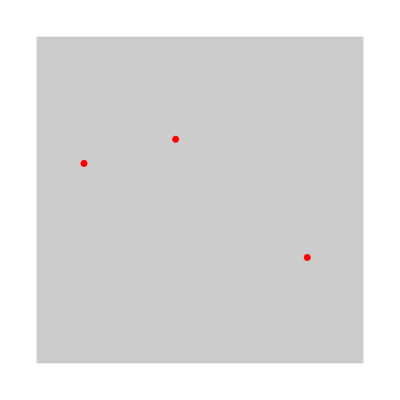

```mathematica
Graphics[{Opacity[0.2],Rectangle[{0,0},{Subscript[ℒ, x],Subscript[ℒ, y]}],Opacity[1],Red,AbsolutePointSize[5],Point@Transpose[{xs,ys}]}]
```

```mathematica
Subscript[ℐ, p_]^:=Subscript[ℐ, p]^=Table[{i,j},{i,p},{j,p}]
```

```mathematica
ArrayFlatten[Outer[Δmat[{Subscript[ℒ, x],Subscript[ℒ, y]}][xs,ys],Subscript[ℐ, p],Subscript[ℐ, p],2]]//TraditionalForm
```

(1.02129 | -0.642928 | 0.0707792 | -0.642928 | 1.09207 | -0.0735973 | 0.0707792 | -0.0735973 | 0.0797762
0.284436 | -0.892894 | -0.12935 | -0.892894 | 0.155087 | 0.00401649 | -0.12935 | 0.00401649 | 0.0959016
0.235445 | 0.698438 | -0.273651 | 0.698438 | -0.0382063 | 0.299711 | -0.273651 | 0.299711 | 0.0854805
0.284436 | -0.892894 | -0.12935 | -0.892894 | 0.155087 | 0.00401649 | -0.12935 | 0.00401649 | 0.0959016
1.25674 | 0.0555099 | -0.202872 | 0.0555099 | 1.05386 | 0.226114 | -0.202872 | 0.226114 | 0.165257
-0.195111 | -0.875305 | -0.475853 | -0.875305 | -0.670964 | 0.236413 | -0.475853 | 0.236413 | 0.171821
0.235445 | 0.698438 | -0.273651 | 0.698438 | -0.0382063 | 0.299711 | -0.273651 | 0.299711 | 0.0854805
-0.195111 | -0.875305 | -0.475853 | -0.875305 | -0.670964 | 0.236413 | -0.475853 | 0.236413 | 0.171821
1.97461 | -0.270428 | -0.285205 | -0.270428 | 1.6894 | 0.287382 | -0.285205 | 0.287382 | 0.26075)

```mathematica
(Sin[(3 π xs)/Subscript[ℒ, x]]Sin[(2 π ys)/Subscript[ℒ, y]]).(Sin[(4 π xs)/Subscript[ℒ, x]]Sin[(2 π ys)/Subscript[ℒ, y]])//Timing
```

{0.000049,4.01669}

```mathematica
Δmat[{Subscript[ℒ, x],Subscript[ℒ, y]}][xs,ys][{3,2},{4,2}]//Timing
```

{0.000425,4.01669}

### Example

Define L_x and L_y as UpValues:

```mathematica
Subscript[ℒ, x]^=5;Subscript[ℒ, y]^=3;
```

Here are the {x_i,y_i} locations of the δ-function spikes:

```mathematica
p=10;
```

```mathematica
xs:=RandomReal[{0,Subscript[ℒ, x]},p]
```

```mathematica
ys:=RandomReal[{0,Subscript[ℒ, y]},p]
```

Here are the locations of the δ-function spikes:

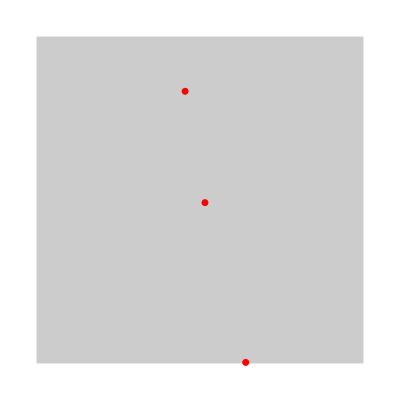

```mathematica
Graphics[{Opacity[0.2],Rectangle[{0,0},{Subscript[ℒ, x],Subscript[ℒ, y]}],Opacity[1],Red,AbsolutePointSize[5],Point@Transpose[{xs,ys}]}]
```

```mathematica
Subscript[ℐ, p_]^:=Subscript[ℐ, p]^=Table[{i,j},{i,p},{j,p}]
```

```mathematica
(Sin[(3 π xs)/Subscript[ℒ, x]]Sin[(2 π ys)/Subscript[ℒ, y]]).(Sin[(4 π xs)/Subscript[ℒ, x]]Sin[(2 π ys)/Subscript[ℒ, y]])//Timing
```

{0.000049,4.01669}

```mathematica
Δmat[{Subscript[ℒ, x],Subscript[ℒ, y]}][xs,ys][{3,2},{4,2}]//Timing
```

{0.000425,4.01669}

```mathematica
∑_(i=1)^Length[xs] Sin[(n π x_⟦i⟧)/Lx]Sin[(m π y_⟦i⟧)/Ly]Sin[(np π x_⟦i⟧)/Lx]Sin[(mp π y_⟦i⟧)/Ly]
```

```mathematica
ArrayFlatten[Outer[Δmat[{Subscript[ℒ, x],Subscript[ℒ, y]}][xs,ys],Subscript[ℐ, Length[xs]],Subscript[ℐ, Length[xs]],2]]
```

$Aborted

### Examples

```mathematica
ArrayFlatten[Outer[f,𝕕,𝕕]]
```

```mathematica
ℂ=Table[Subscript[c, i,j],{i,3},{j,3}]
```

{{c_(1,1),c_(1,2),c_(1,3)},{c_(2,1),c_(2,2),c_(2,3)},{c_(3,1),c_(3,2),c_(3,3)}}

```mathematica
𝕕=Table[Subscript[d, i,j],{i,3},{j,3}]
```

{{d_(1,1),d_(1,2),d_(1,3)},{d_(2,1),d_(2,2),d_(2,3)},{d_(3,1),d_(3,2),d_(3,3)}}

```mathematica
ArrayFlatten[Outer[f,𝕕,𝕕]]//TraditionalForm
```

(f(d_(1,1),d_(1,1)) | f(d_(1,1),d_(1,2)) | f(d_(1,1),d_(1,3)) | f(d_(1,2),d_(1,1)) | f(d_(1,2),d_(1,2)) | f(d_(1,2),d_(1,3)) | f(d_(1,3),d_(1,1)) | f(d_(1,3),d_(1,2)) | f(d_(1,3),d_(1,3))
f(d_(1,1),d_(2,1)) | f(d_(1,1),d_(2,2)) | f(d_(1,1),d_(2,3)) | f(d_(1,2),d_(2,1)) | f(d_(1,2),d_(2,2)) | f(d_(1,2),d_(2,3)) | f(d_(1,3),d_(2,1)) | f(d_(1,3),d_(2,2)) | f(d_(1,3),d_(2,3))
f(d_(1,1),d_(3,1)) | f(d_(1,1),d_(3,2)) | f(d_(1,1),d_(3,3)) | f(d_(1,2),d_(3,1)) | f(d_(1,2),d_(3,2)) | f(d_(1,2),d_(3,3)) | f(d_(1,3),d_(3,1)) | f(d_(1,3),d_(3,2)) | f(d_(1,3),d_(3,3))
f(d_(2,1),d_(1,1)) | f(d_(2,1),d_(1,2)) | f(d_(2,1),d_(1,3)) | f(d_(2,2),d_(1,1)) | f(d_(2,2),d_(1,2)) | f(d_(2,2),d_(1,3)) | f(d_(2,3),d_(1,1)) | f(d_(2,3),d_(1,2)) | f(d_(2,3),d_(1,3))
f(d_(2,1),d_(2,1)) | f(d_(2,1),d_(2,2)) | f(d_(2,1),d_(2,3)) | f(d_(2,2),d_(2,1)) | f(d_(2,2),d_(2,2)) | f(d_(2,2),d_(2,3)) | f(d_(2,3),d_(2,1)) | f(d_(2,3),d_(2,2)) | f(d_(2,3),d_(2,3))
f(d_(2,1),d_(3,1)) | f(d_(2,1),d_(3,2)) | f(d_(2,1),d_(3,3)) | f(d_(2,2),d_(3,1)) | f(d_(2,2),d_(3,2)) | f(d_(2,2),d_(3,3)) | f(d_(2,3),d_(3,1)) | f(d_(2,3),d_(3,2)) | f(d_(2,3),d_(3,3))
f(d_(3,1),d_(1,1)) | f(d_(3,1),d_(1,2)) | f(d_(3,1),d_(1,3)) | f(d_(3,2),d_(1,1)) | f(d_(3,2),d_(1,2)) | f(d_(3,2),d_(1,3)) | f(d_(3,3),d_(1,1)) | f(d_(3,3),d_(1,2)) | f(d_(3,3),d_(1,3))
f(d_(3,1),d_(2,1)) | f(d_(3,1),d_(2,2)) | f(d_(3,1),d_(2,3)) | f(d_(3,2),d_(2,1)) | f(d_(3,2),d_(2,2)) | f(d_(3,2),d_(2,3)) | f(d_(3,3),d_(2,1)) | f(d_(3,3),d_(2,2)) | f(d_(3,3),d_(2,3))
f(d_(3,1),d_(3,1)) | f(d_(3,1),d_(3,2)) | f(d_(3,1),d_(3,3)) | f(d_(3,2),d_(3,1)) | f(d_(3,2),d_(3,2)) | f(d_(3,2),d_(3,3)) | f(d_(3,3),d_(3,1)) | f(d_(3,3),d_(3,2)) | f(d_(3,3),d_(3,3)))

```mathematica
ArrayFlatten[Outer[f,𝕕,𝕕]].ArrayFlatten[ℂ,1]//TraditionalForm
```

{f(d_(1,1),d_(1,1)) c_(1,1)+f(d_(1,1),d_(1,2)) c_(1,2)+f(d_(1,1),d_(1,3)) c_(1,3)+f(d_(1,2),d_(1,1)) c_(2,1)+f(d_(1,2),d_(1,2)) c_(2,2)+f(d_(1,2),d_(1,3)) c_(2,3)+f(d_(1,3),d_(1,1)) c_(3,1)+f(d_(1,3),d_(1,2)) c_(3,2)+f(d_(1,3),d_(1,3)) c_(3,3),f(d_(1,1),d_(2,1)) c_(1,1)+f(d_(1,1),d_(2,2)) c_(1,2)+f(d_(1,1),d_(2,3)) c_(1,3)+f(d_(1,2),d_(2,1)) c_(2,1)+f(d_(1,2),d_(2,2)) c_(2,2)+f(d_(1,2),d_(2,3)) c_(2,3)+f(d_(1,3),d_(2,1)) c_(3,1)+f(d_(1,3),d_(2,2)) c_(3,2)+f(d_(1,3),d_(2,3)) c_(3,3),f(d_(1,1),d_(3,1)) c_(1,1)+f(d_(1,1),d_(3,2)) c_(1,2)+f(d_(1,1),d_(3,3)) c_(1,3)+f(d_(1,2),d_(3,1)) c_(2,1)+f(d_(1,2),d_(3,2)) c_(2,2)+f(d_(1,2),d_(3,3)) c_(2,3)+f(d_(1,3),d_(3,1)) c_(3,1)+f(d_(1,3),d_(3,2)) c_(3,2)+f(d_(1,3),d_(3,3)) c_(3,3),f(d_(2,1),d_(1,1)) c_(1,1)+f(d_(2,1),d_(1,2)) c_(1,2)+f(d_(2,1),d_(1,3)) c_(1,3)+f(d_(2,2),d_(1,1)) c_(2,1)+f(d_(2,2),d_(1,2)) c_(2,2)+f(d_(2,2),d_(1,3)) c_(2,3)+f(d_(2,3),d_(1,1)) c_(3,1)+f(d_(2,3),d_(1,2)) c_(3,2)+f(d_(2,3),d_(1,3)) c_(3,3),f(d_(2,1),d_(2,1)) c_(1,1)+f(d_(2,1),d_(2,2)) c_(1,2)+f(d_(2,1),d_(2,3)) c_(1,3)+f(d_(2,2),d_(2,1)) c_(2,1)+f(d_(2,2),d_(2,2)) c_(2,2)+f(d_(2,2),d_(2,3)) c_(2,3)+f(d_(2,3),d_(2,1)) c_(3,1)+f(d_(2,3),d_(2,2)) c_(3,2)+f(d_(2,3),d_(2,3)) c_(3,3),f(d_(2,1),d_(3,1)) c_(1,1)+f(d_(2,1),d_(3,2)) c_(1,2)+f(d_(2,1),d_(3,3)) c_(1,3)+f(d_(2,2),d_(3,1)) c_(2,1)+f(d_(2,2),d_(3,2)) c_(2,2)+f(d_(2,2),d_(3,3)) c_(2,3)+f(d_(2,3),d_(3,1)) c_(3,1)+f(d_(2,3),d_(3,2)) c_(3,2)+f(d_(2,3),d_(3,3)) c_(3,3),f(d_(3,1),d_(1,1)) c_(1,1)+f(d_(3,1),d_(1,2)) c_(1,2)+f(d_(3,1),d_(1,3)) c_(1,3)+f(d_(3,2),d_(1,1)) c_(2,1)+f(d_(3,2),d_(1,2)) c_(2,2)+f(d_(3,2),d_(1,3)) c_(2,3)+f(d_(3,3),d_(1,1)) c_(3,1)+f(d_(3,3),d_(1,2)) c_(3,2)+f(d_(3,3),d_(1,3)) c_(3,3),f(d_(3,1),d_(2,1)) c_(1,1)+f(d_(3,1),d_(2,2)) c_(1,2)+f(d_(3,1),d_(2,3)) c_(1,3)+f(d_(3,2),d_(2,1)) c_(2,1)+f(d_(3,2),d_(2,2)) c_(2,2)+f(d_(3,2),d_(2,3)) c_(2,3)+f(d_(3,3),d_(2,1)) c_(3,1)+f(d_(3,3),d_(2,2)) c_(3,2)+f(d_(3,3),d_(2,3)) c_(3,3),f(d_(3,1),d_(3,1)) c_(1,1)+f(d_(3,1),d_(3,2)) c_(1,2)+f(d_(3,1),d_(3,3)) c_(1,3)+f(d_(3,2),d_(3,1)) c_(2,1)+f(d_(3,2),d_(3,2)) c_(2,2)+f(d_(3,2),d_(3,3)) c_(2,3)+f(d_(3,3),d_(3,1)) c_(3,1)+f(d_(3,3),d_(3,2)) c_(3,2)+f(d_(3,3),d_(3,3)) c_(3,3)}

```mathematica
Flatten[𝕕.Outer[List,𝒞,𝒞,1],2]//TraditionalForm
```

(c_(1,1) d_(1,1)+c_(2,1) d_(1,2) | c_(1,2) d_(1,1)+c_(2,2) d_(1,2)
c_(1,1) d_(1,1)+c_(1,1) d_(1,2) | c_(1,2) d_(1,1)+c_(1,2) d_(1,2)
c_(1,1) d_(1,1)+c_(2,1) d_(1,2) | c_(1,2) d_(1,1)+c_(2,2) d_(1,2)
c_(2,1) d_(1,1)+c_(2,1) d_(1,2) | c_(2,2) d_(1,1)+c_(2,2) d_(1,2)
c_(1,1) d_(2,1)+c_(2,1) d_(2,2) | c_(1,2) d_(2,1)+c_(2,2) d_(2,2)
c_(1,1) d_(2,1)+c_(1,1) d_(2,2) | c_(1,2) d_(2,1)+c_(1,2) d_(2,2)
c_(1,1) d_(2,1)+c_(2,1) d_(2,2) | c_(1,2) d_(2,1)+c_(2,2) d_(2,2)
c_(2,1) d_(2,1)+c_(2,1) d_(2,2) | c_(2,2) d_(2,1)+c_(2,2) d_(2,2))

```mathematica
Flatten[Outer[List,𝒞,𝒞,2].𝕕,3]//TraditionalForm
```

(c_(1,1) d_(1,1)+c_(1,1) d_(2,1) | c_(1,1) d_(1,2)+c_(1,1) d_(2,2)
c_(1,1) d_(1,1)+c_(1,2) d_(2,1) | c_(1,1) d_(1,2)+c_(1,2) d_(2,2)
c_(1,1) d_(1,1)+c_(2,1) d_(2,1) | c_(1,1) d_(1,2)+c_(2,1) d_(2,2)
c_(1,1) d_(1,1)+c_(2,2) d_(2,1) | c_(1,1) d_(1,2)+c_(2,2) d_(2,2)
c_(1,2) d_(1,1)+c_(1,1) d_(2,1) | c_(1,2) d_(1,2)+c_(1,1) d_(2,2)
c_(1,2) d_(1,1)+c_(1,2) d_(2,1) | c_(1,2) d_(1,2)+c_(1,2) d_(2,2)
c_(1,2) d_(1,1)+c_(2,1) d_(2,1) | c_(1,2) d_(1,2)+c_(2,1) d_(2,2)
c_(1,2) d_(1,1)+c_(2,2) d_(2,1) | c_(1,2) d_(1,2)+c_(2,2) d_(2,2)
c_(2,1) d_(1,1)+c_(1,1) d_(2,1) | c_(2,1) d_(1,2)+c_(1,1) d_(2,2)
c_(2,1) d_(1,1)+c_(1,2) d_(2,1) | c_(2,1) d_(1,2)+c_(1,2) d_(2,2)
c_(2,1) d_(1,1)+c_(2,1) d_(2,1) | c_(2,1) d_(1,2)+c_(2,1) d_(2,2)
c_(2,1) d_(1,1)+c_(2,2) d_(2,1) | c_(2,1) d_(1,2)+c_(2,2) d_(2,2)
c_(2,2) d_(1,1)+c_(1,1) d_(2,1) | c_(2,2) d_(1,2)+c_(1,1) d_(2,2)
c_(2,2) d_(1,1)+c_(1,2) d_(2,1) | c_(2,2) d_(1,2)+c_(1,2) d_(2,2)
c_(2,2) d_(1,1)+c_(2,1) d_(2,1) | c_(2,2) d_(1,2)+c_(2,1) d_(2,2)
c_(2,2) d_(1,1)+c_(2,2) d_(2,1) | c_(2,2) d_(1,2)+c_(2,2) d_(2,2))

```mathematica
index[{n_,m_,i_:4}]:=(n-1) i+m
```

```mathematica
Table[index[{i,j}],{i,4},{j,4}]
```

{{1,2,3,4},{5,6,7,8},{9,10,11,12},{13,14,15,16}}

```mathematica
Flatten[𝒞,1]
```

{c_(1,1),c_(1,2),c_(1,3),c_(1,4),c_(2,1),c_(2,2),c_(2,3),c_(2,4),c_(3,1),c_(3,2),c_(3,3),c_(3,4),c_(4,1),c_(4,2),c_(4,3),c_(4,4)}

```mathematica
∑_n ∑_m Subscript[C, {n,m}] Subscript[Δ, {n,m},{np,mp}]
```

```mathematica
∑_k Subscript[C, k] Subscript[Δ, k,kp]
```

```mathematica
Subscript[Δ, {n_,m_},{np_,mp_}]:=δ[index[{n,m}],index[{np,mp}]]
```

```mathematica
Subscript[Δ, {1,2},{1,1}]
```

δ[2,1]

```mathematica
Subscript[Δ, {2,1},{1,2}]
```

δ[5,2]

```mathematica
Subscript[𝒸, {n_,m_}]:=𝕔[index[{n,m}]]
```

```mathematica
Subscript[𝒸, {2,3}]
```

𝕔[7]

```mathematica
index[{2,1}]
```

5